Номер 5
Условие:
Используя таблицу значений функции f(x) в равноотстоящих точках
отрезка [0, 6], полученной в задании 1 при n = 10, выполнить следующие действия:
а) аппроксимировать с помощью метода наименьших квадратов функциюf(x) многочленом первой степени Q_1(x), проиллюстрировать
графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Q_1(x) на одном чертеже);
б) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом второйстепениQ_2(x), проиллюстрировать
графически;
в) найти многочлены наилучшего среднеквадратичного приближения
третьей и четвертой степеней(Q_3(x) и Q_4(x)) с помощью функции Fit
пакета Mathematica, проиллюстрировать графически;
г) вычислить значения функции f(x) и построенных многочленов Q_1(x), Q_2(x), Q_3(x) и Q_4(x) в точке x = 2,4316;
д) сравнить результаты, полученные впунктах а, б и в, изобразив на одном чертеже точки (x_i, f(x_i)) и графики функций Q_1(x), Q_2(x), Q_3(x) и Q_4(x).

Функция f(x):

```mathematica
f[x_]=3+(2/7 x-Cosh[(3x)/13]) Log[x^2+2 x+3]
```

3+((2 x)/7-Cosh[(3 x)/13]) Log[3+2 x+x^2]

Значения из условия задания и шаг интерполяции h для равноотстоящих узлов:

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

Возьмём таблицу значений функции для равноотстоящих узлов на промежутке для n = 10:

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
```

```mathematica
TableForm[data]
```

0. | 1.90139
0.6 | 1.72822
1.2 | 1.66226
1.8 | 1.68933
2.4 | 1.77043
3. | 1.86632
3.6 | 1.94154
4.2 | 1.96364
4.8 | 1.90147
5.4 | 1.72369
6. | 1.39751

а)

Степень многочлена, которым будет аппроксимирована функция:

```mathematica
m=1;
```

Коэффициенты каждой строки системы относительно a_i:

```mathematica
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

Столбец свободных членов:

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B1
```

{19.5458,57.9773}

Найдём значения a_i с помощью встроенной функции LinearSolve:

```mathematica
A1=LinearSolve[ACoeff1,B1]
```

{1.8269,-0.0166687}

Тогда многочлен примет вид:

```mathematica
Q1[x_]=∑_(i=0)^m (A1[[i+1]]*x^i)
```

1.8269-0.0166687 x

Изобразим полученный многочлен:

```mathematica
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Yellow];
```

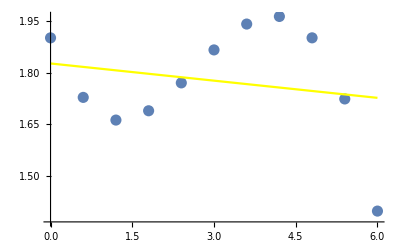

```mathematica
Show[graphD,graphQ1]
```

б)

Аналогичным образом найдём многочлен второй степени.

```mathematica
m=2;
```

```mathematica
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B2
```

{19.5458,57.9773,239.668}

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{1.69827,0.126251,-0.02382}

Многочлен примет вид:

```mathematica
Q2[x_]=∑_(i=0)^m (A2[[i+1]]*x^i)
```

1.69827+0.126251 x-0.02382 x^2

Изобразим полученный многочлен:

```mathematica
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Orange];
```

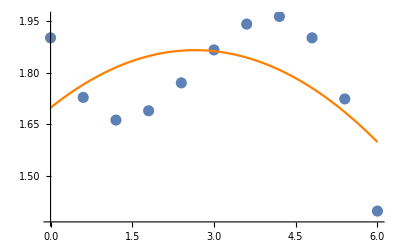

```mathematica
Show[graphD,graphQ2]
```

в)

Построим многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней с помощью встроенной функции Fit:

```mathematica
Q3[x_]=Fit[data,{1,x^1,x^2,x^3},x]
```

1.90146-0.411836 x+0.211358 x^2-0.0261309 x^3

```mathematica
Q4[x_]=Fit[data,{1,x^1,x^2,x^3,x^4},x]
```

1.9034-0.423053 x+0.220705 x^2-0.0286235 x^3+0.000207713 x^4

Изобразим полученные многочлены:

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->{Green,Thickness[0.01]}];
```

```mathematica
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Red];
```

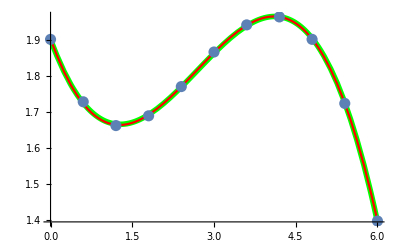

```mathematica
Show[graphQ3,graphQ4,graphD]
```

г)

Значения полученных многочленов в точке x0:

```mathematica
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=1.78636, Q2[x0]=1.86442, Q3[x0]=1.77404, Q4[x0]=1.7754

д)

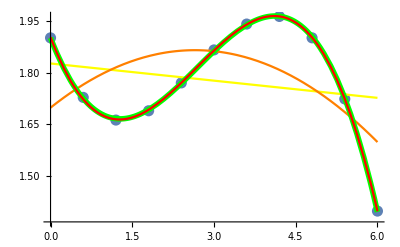

```mathematica
Show[graphD,graphQ1,graphQ2,graphQ3,graphQ4]
```

Как видно из графика, с увеличением степени многочлена аппроксимация методом наименьших квадратов даёт значения, всё более близкие к значениям исходной функции.